# Ingesting CDR Data and Visualising Key Influencers within the Network

Communication service providers produce large volumes of calling data records (CDR) every minute day in and out. The analysis of relationships between customers is important to detect key call influencers and non-influencers..

## Curated CDR Data Call detail records (CDR) datasets includes the time, duration, caller and callee, and the locations of the cellular towers depending on the network configuration. The current set of CDR has the call time, Calling Number, called Number, Call Forwarded Number, Call Duration, Call Type, Call Answered Status..etc

```mathematica
Code (* Try to make simple visualizations when possible to illustrate the topic and create visual interest. *)
```

Code

```mathematica
cdrdata=Import["/Users/jassimmoideen/Desktop/WSS2017/CDR2.csv","Table","FieldSeparators"->{","}];
Dataset[cdrdata]
```

Dataset[<>]

### To identify brand influencers among customers Telecom marketing normally involves expensive viral marketing campaign that might work or fail. Based on the success most of them are repeated blindly to achieve a similar past success. This process done doesn’t identify the influence of the existing customers. This might not only fail because the wrong persons are targeted but also when no influence exists for a particular product or market. However, once a network of influence is detected, we can identify the influencers based on historical data. Even when no obvious social network exists, a social network can be constructed using the call transactions as long as those call transactions capture also the name of the customer.Once a network is constructed based on the call transactions, the classic social network algorithms can be applied to identify the influencers to be used in a CVM marketing campaign. It is based on the Word Of Mouth (WOM) process, where good (and bad) experiences with product and services are shared with friends, colleagues and relatives. And in turn, those people will share the same message with their social network. One way to conduct the marketing campaign is to identify a segmented customer population and target them with a marketing message which might include free product samples or promotion offers. To reduce the campaign cost, the target population needs to be selected carefully. Marketing campaigns could target customers with a high Customer Lifetime Value (CLV), which is often defined as the expected profit from sales during the lifetime of the relationship between the customer and the company. But this measurement ignores the influence customers have on the buying behaviour of others. Influencing buying behaviour through word of mouth is a proven phenomenon shown by studies where promotors might influence other people belonging to their social network at buying or subscribing products specifically recommended by their influencers. These influencers are neither celebrities nor customers with a high CLV and are therefore not detected by the marketing department. This approach help marketing CVM departments to detect if a network of influence exists for a particular customer segment or product. Selecting the customers that are influencers for specific products among your customer database. Beside identifying which customers are influencers, we can also select those influencers that have proven to be influencers for a particular product category with very specific selection of influencers can be made, e.g. influencers of a particular product or product group. This information can then be used for a cross-sell or up-sell marketing campaign.

```mathematica
edges=Map[#[[2]]->#[[3]]&,cdrdata]
```

{CALLING NUMBER→CALLED NUMBER,4045551212→4041212555,9195551212→8191212555,8045551212→5401212555,2705551212→8151212555,9735551212→8121212555,2145551212→8121212555,3525551212→6151212555,5615551212→8191212555,5185551212→5181212555,8175551212→9091212555,5615551212→8161212555,8155551212→8181212555,7135551212→8181212555,6155551212→8161212555,7175551212→7171212555,4075551212→8141212555,2145551212→8161212555,8455551212→8451212555,6785551212→4041212555,5125551212→2101212555,9515551212→9091212555,7145551212→9091212555,2025551212→4101212555,7855551212→7021212555,9545551212→9541212555,4045551212→4041212555,9545551212→8001212555,9095551212→9091212555,3035551212→8001212555,7025551212→9091212555,5595551212→9091212555,6155551212→6151212555,6785551212→4041212555,9735551212→8001212555,2705551212→6151212555,5405551212→5401212555,6025551212→7021212555,4705551212→4041212555,9515551212→8001212555,4075551212→4071212555,8015551212→7141212555,8175551212→8001212555,2405551212→4101212555,2145551212→4041212555,4045551212→4041212555,7605551212→8001212555,4045551212→4041212555,7705551212→4041212555,7705551212→4041212555,9195551212→4041212555}

```mathematica
Graph[edges]
```

-Graphics-

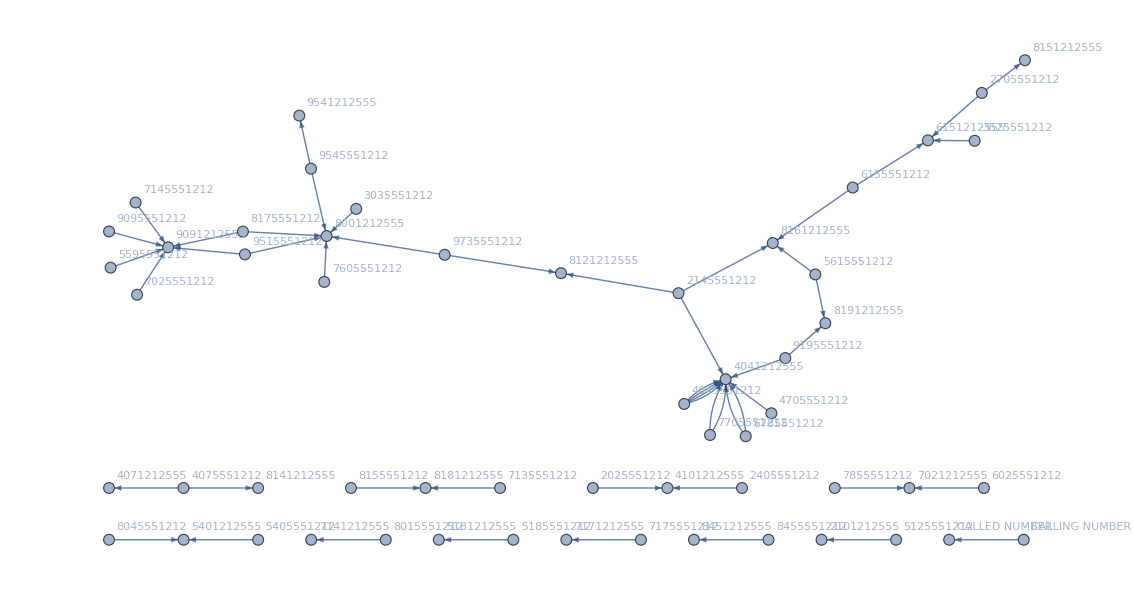

```mathematica
Graph[edges,VertexLabels->"Name"]
```

```mathematica
DegreeCentrality[edges]
```

{1,1,1,6,2,2,1,2,2,1,2,2,3,1,3,2,1,1,2,6,3,1,2,1,2,1,1,2,1,1,1,1,1,1,2,1,1,2,1,2,2,1,6,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
HighlightGraph[edges,VertexList[edges],VertexSize->Thread[VertexList[edges]->Rescale[%]]]
```

-Graphics-

Rank vertices. Highest-ranked vertices have the most connections to other vertices:

```mathematica
Part[VertexList[edges],Ordering[DegreeCentrality[edges],All,Greater]]
```

{8001212555,9091212555,4041212555,8161212555,6151212555,2145551212,9545551212,7021212555,4101212555,9515551212,4075551212,6155551212,8181212555,8175551212,5615551212,8121212555,9735551212,2705551212,5401212555,8191212555,9195551212,7705551212,7605551212,2405551212,7141212555,8015551212,4071212555,4705551212,6025551212,5405551212,5595551212,7025551212,3035551212,9095551212,9541212555,7855551212,2025551212,7145551212,2101212555,5125551212,6785551212,8451212555,8455551212,8141212555,7171212555,7175551212,7135551212,8155551212,5181212555,5185551212,3525551212,8151212555,8045551212,4045551212,CALLED NUMBER,CALLING NUMBER}

Further Explorations

Churn Detection

Social Network Analysis of Mobile Data Usage

Authorship information

Jassim Moideen

23rd June 2017

jassim.moideen@gmail.com